## Problem 5: Fourier Series

```mathematica
f[k_,t_]=1/(√(2π))ⅇ^(ⅈ k t);
f[t_]=2t+1;
```

### (a) Verify that each f_k has norm 1.

```mathematica
Table[{StringTemplate["k = ``"][k],
√(∫_0^(2π) f[k,t](f[k,t]*)ⅆt)},{k,-5,5}]//MatrixForm
```

(k = -5 | 1
k = -4 | 1
k = -3 | 1
k = -2 | 1
k = -1 | 1
k = 0 | 1
k = 1 | 1
k = 2 | 1
k = 3 | 1
k = 4 | 1
k = 5 | 1)

### (b) Verify that f_k and f_j are orthogonal if k ≠ j

```mathematica
Assuming[k≠j&&k∈Integers&&j∈Integers,
 ∫_0^(2π) f[k,t](f[j,t]*)ⅆt]
```

0

### (c) Compute α_k=⟨f,f_k⟩ for k = 0, ±1, ±2, ±3, ±4, ±5

```mathematica
α[k_]:=∫_0^(2π) f[t](f[k,t]*)ⅆt;
Table[{StringTemplate["α_(``) = "][k],α[k]},
{k,-5,5}]//MatrixForm
```

(α_-5 =  | -2/5 ⅈ √(2 π)
α_-4 =  | -ⅈ √(π/2)
α_-3 =  | -2/3 ⅈ √(2 π)
α_-2 =  | -ⅈ √(2 π)
α_-1 =  | -2 ⅈ √(2 π)
α_0 =  | 2 √2 π^(3/2)+√(2 π)
α_1 =  | 2 ⅈ √(2 π)
α_2 =  | ⅈ √(2 π)
α_3 =  | 2/3 ⅈ √(2 π)
α_4 =  | ⅈ √(π/2)
α_5 =  | 2/5 ⅈ √(2 π))

### (d) Compute the partial sums:

```mathematica
g[n_,t_]:=∑_(k=-n)^n α[k]f[k,t];
partialSums=Table[{StringTemplate["g_(``)(t) = "][n],g[n,t]},
{n,0,5}]//FullSimplify//Expand;
partialSums//MatrixForm
```

(g_0(t) =  | 1+2 π
g_1(t) =  | 1+2 π-4 Sin[t]
g_2(t) =  | 1+2 π-4 Sin[t]-2 Sin[2 t]
g_3(t) =  | 1+2 π-4 Sin[t]-2 Sin[2 t]-4/3 Sin[3 t]
g_4(t) =  | 1+2 π-4 Sin[t]-2 Sin[2 t]-4/3 Sin[3 t]-Sin[4 t]
g_5(t) =  | 1+2 π-4 Sin[t]-2 Sin[2 t]-4/3 Sin[3 t]-Sin[4 t]-4/5 Sin[5 t])

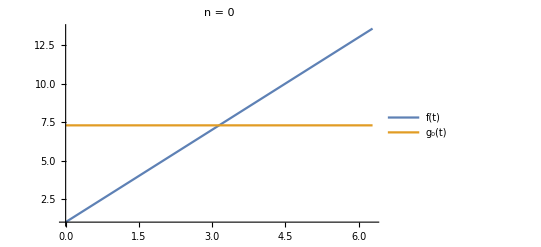
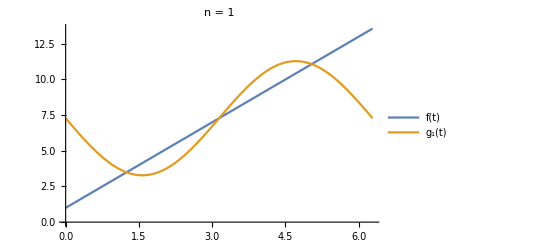
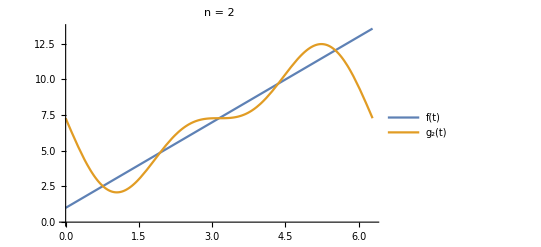
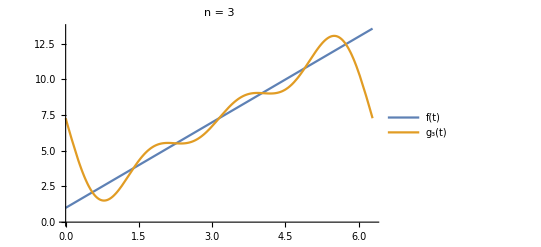
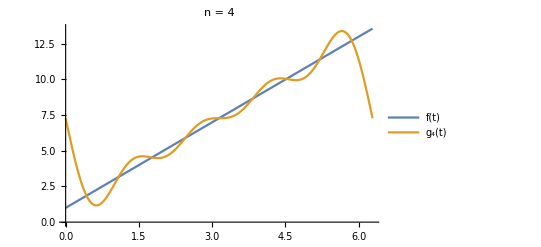
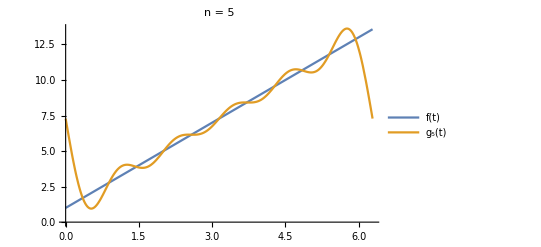
(-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
ArrayReshape[Table[
Plot[{f[t],partialSums⟦i,2⟧},{t,0,2π},
PlotLabel->StringTemplate["n = ``"][i-1],
PlotLegends->{"f(t)", StringTemplate["g_(``)(t)"][i-1]}],
{i,1,6}],{3,2}]//MatrixForm
```

### (e) What is ||f(||)_2^2 and ∑_(k=-5)^5 |α_k|^2?

```mathematica
∫_0^(2π) f[t](f[t]*)ⅆt//N
∑_(k=-5)^5 Abs[α[k]]^2//N
```

415.974

406.859

### (f) For each value of n = 0,1,2,3,4,5, compute L_2-error.

```mathematica
Table[{StringTemplate["||f - g_(``)(||)_2 = "][n],√(∫_0^(2π) (f[t]-partialSums⟦n+1,2⟧)((f[t]-partialSums⟦n+1,2⟧)*)ⅆt)},{n,0,5}]//N//MatrixForm
```

(||f - g_0(||)_2 =  | 9.09304
||f - g_1(||)_2 =  | 5.69367
||f - g_2(||)_2 =  | 4.45551
||f - g_3(||)_2 =  | 3.7771
||f - g_4(||)_2 =  | 3.3354
||f - g_5(||)_2 =  | 3.01899)

### What is the “max norm” error ||f-g_n(||)_∞=max_(t∈[0,2π]) |f(t)-g_n(t)|?

```mathematica
Table[{StringTemplate["n = ``"][n],
Maximize[{Abs[f[t]-partialSums⟦n+1,2⟧],
0≤t≤2π},t]},
{n,0,5}]//MatrixForm
```

(n = 0 | {2 π,{t→0}}
n = 1 | {2 π,{t→0}}
n = 2 | {2 π,{t→0}}
n = 3 | {2 π,{t→0}}
n = 4 | {2 π,{t→0}}
n = 5 | {2 π,{t→0}})